# Hermite Function He_n(x)

## Physicist Hermite Polynomial H_n(x)

```mathematica
HermiteH[0, x]
```

1

```mathematica
HermiteH[1, x]
```

2 x

```mathematica
HermiteH[2, x]
```

-2+4 x^2

## Probabilists Hermite Polynomial He_n(x)

```mathematica
HermiteHe[n_, x_]:=(2^(-n/2))*HermiteH[n, x/(2^0.5)]
```

```mathematica
HermiteHe[2, x] //Simplify
```

-1.+1. x^2

```mathematica
HermiteHe[1, x]
```

1. x

```mathematica
HermiteHe[5, x] //Simplify
```

15. x-10. x^3+1. x^5

## Plotting

```mathematica
FewHermites = Table[HermiteH[n, x], {n, 0, 5}]
```

{1,2 x,-2+4 x^2,-12 x+8 x^3,12-48 x^2+16 x^4,120 x-160 x^3+32 x^5}

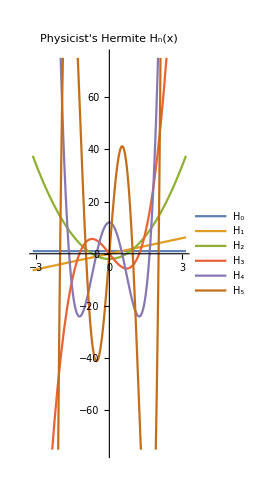

```mathematica
Plot[FewHermites,{x, -Pi, +Pi},PlotLabel->"Physicist's Hermite H_n(x)",PlotLegends->{Table[Subscript[H, n], {n, 0, 5}]}, PlotRange->{{-Pi, Pi}, {-75, 75}}, AspectRatio->Full]
```

```mathematica
FewHermitesHe = Table[HermiteHe[n, x],{n, 0, 5}]
```

{1,1. x,1/2 (-2.+2. x^2),(-8.48528 x+2.82843 x^3)/(2 √2),1/4 (12.-24. x^2+4. x^4),(84.8528 x-56.5685 x^3+5.65685 x^5)/(4 √2)}

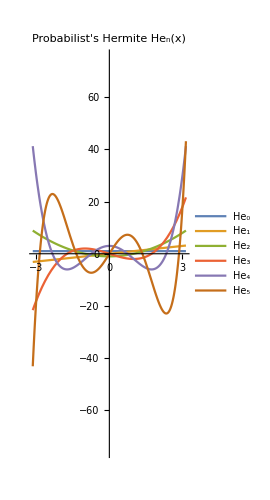

```mathematica
Plot[FewHermitesHe, {x, -Pi, Pi},PlotLabel->"Probabilist's Hermite He_n(x)",PlotLegends->{Table[Subscript[He, n], {n, 0, 5}]}, PlotRange->{{-Pi, Pi}, {-75, 75}}, AspectRatio->Full]
```

Note that the plots of He_n(x) are spread out more than those of H_n(x), because He_n(x) = 2^(-n/2)*H_n(x/√2), i.e. vertically compressing the plots of H_n(x) by a factor of √2^n and horizontally stretching the plots of H_n(x) by √2 or compressing the x-axis by the same factor.

## Orthogonality

```mathematica
Integrate[He[0, x]*He[1, x]*e^(-x^2/2), {x, -∞, +∞}]
```

ConditionalExpression[0., Re[Log[e]]>0]

```mathematica
Integrate[He[0, x]*He[0, x]*e^(-x^2/2), {x, -∞, +∞}]
```

ConditionalExpression[(√(2 π))/(√Log[e]), Re[Log[e]]>0]

```mathematica
Integrate[He[1, x]*He[1, x]*e^(-x^2/2), {x, -∞, +∞}]
```

ConditionalExpression[2.50663/Log[e]^(3/2), Re[Log[e]]>0]

## Derivatives

```mathematica
FewDerivatives = Simplify[D[FewHermitesHe, x]]
```

{0,1.,2. x,-3.+3. x^2,-12. x+4. x^3,15.-30. x^2+5. x^4}

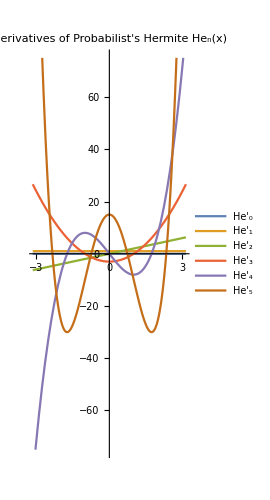

```mathematica
Plot[FewDerivatives, {x, -Pi, +Pi}, PlotLabel->"Derivatives of Probabilist's Hermite He_n(x)",PlotLegends->{Table[Subscript[He', n], {n, 0, 5}]}, PlotRange->{{-Pi, Pi}, {-75, 75}}, AspectRatio->Full]
```